```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/norbert/Dropbox (MIT)/StasPacking/Data/eqSpheres

This is the place where the figures are saved for inclusion in the paper. Not for data!

```mathematica
FigDir="/Users/norbert/Dropbox (MIT)/StasPacking/figure_data/";
```

Adjacency data for the Thompson problem - there are two almost equivalent graphs (almost same energy, therefore both are very likely as solutions of the Thomson problem):

```mathematica
TADJ=Import["../Thomson/ADJ_Thomson11.mat"]//First;
TV = Import["../Thomson/Thomson11.mat"];
V=TV[[3]];
cHull=ConvexHullMesh[V];
ThomsonGraph=AdjacencyGraph[Round[TADJ]];
a1=GraphAutomorphismGroup[ThomsonGraph];
NAutThomson=GroupOrder[a1];
```

```mathematica
TADJ2=Import["../Thomson/ADJ_Thomson2.mat"]//First;
TV = Import["../Thomson/Thomson2.mat"];
V2=TV[[3]];
cHull2=ConvexHullMesh[V2];
ThomsonGraph2=AdjacencyGraph[Round[TADJ2]];
a2=GraphAutomorphismGroup[ThomsonGraph2];
NAutThomson2=GroupOrder[a2];
```

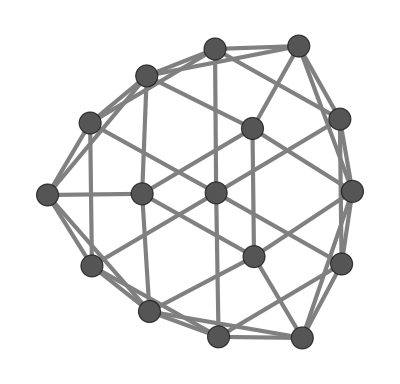

```mathematica
T0Planar=Graph[ThomsonGraph,EdgeStyle->Directive[{AbsoluteThickness[3],Gray,Opacity[1]}],VertexSize->0.3,VertexStyle->Darker[Gray]]
```

```mathematica
Export[FigDir<>"/Thomson_T0_PlanarGraph"<>ToString[p]<>".pdf",T0Planar,"AllowRasterization"->False];
```

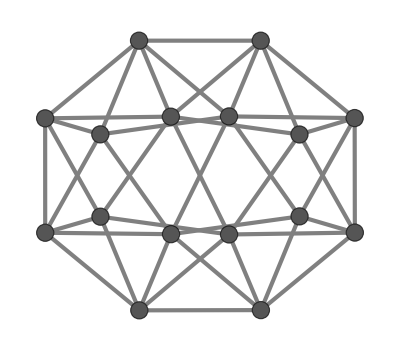

```mathematica
T1Planar=Graph[ThomsonGraph2,EdgeStyle->Directive[{AbsoluteThickness[3],Gray,Opacity[1]}],VertexSize->0.3,VertexStyle->Darker[Gray]]
```

```mathematica
Export[FigDir<>"/Thomson_T1_PlanarGraph"<>ToString[p]<>".pdf",T1Planar,"AllowRasterization"->False];
```

```mathematica
Graph
```

```mathematica
{ThomsonGraph,ThomsonGraph2}
```

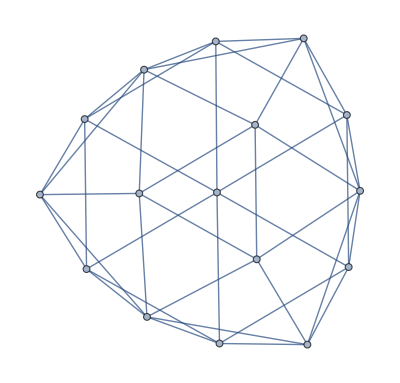
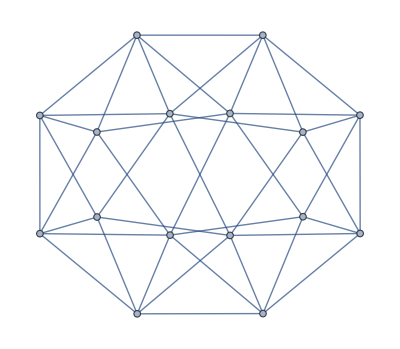

Graphs 1 has 24 automorphism groups :

```mathematica
NAutThomson
```

24

```mathematica
NAutThomson2
```

4

This is the ring canal tree:

```mathematica
RCAdj=Round[Import["RCAdj.mat"][[1]]];
GRC=AdjacencyGraph[RCAdj];
RCa=GraphAutomorphismGroup[GRC];
NAutRC=GroupOrder[RCa];
```

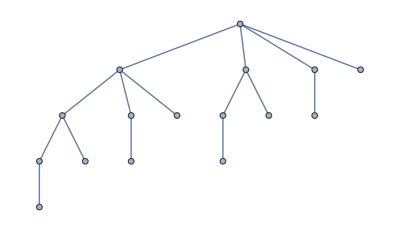

```mathematica
GRC
```

```mathematica
NAutRC
```

2

## Plot the representative Thomson configurations from simulations:

```mathematica
Configs=Import["ThomsonRepConfigs.mat"];
(* By convention, we call T0 the graph with 24 automorphisms. Therefore we need to relabel the two graphs*)
X1=Configs[[2]]/2.4;
CoordRule1=Table[i->X1[[i]],{i,1,16}];
X2=Configs[[1]]/2.4;
CoordRule2=Table[i->X2[[i]],{i,1,16}];
GD=Import["../GD_Mathematica.mat"]//First//First;
MyColors=Import["../MyColors_Mathematica.mat"]//First;
```

```mathematica
SPS=Table[{Opacity[1],RGBColor[MyColors[[GD[[i]]+1]]],Sphere[X1[[i]],0.085]},{i,1,16}];
cHull=ConvexHullMesh[X1];
SPS2=Table[{Opacity[1],RGBColor[0.5,0.5,0.5],Sphere[X2[[i]],0.085]},{i,1,16}];
cHull2=ConvexHullMesh[X2];
```

```mathematica
T1=Show[HighlightMesh[cHull,{Style[1,AbsoluteThickness[10], Black, Opacity[0.5]], Style[2,Opacity[0.5]]}],
GraphPlot3D[GRC, VertexCoordinateRules->CoordRule1,
VertexRenderingFunction->({RGBColor[MyColors[[GD[[#2]]+1]]],Sphere[#1,0.085]}&),
EdgeRenderingFunction->({RGBColor[0.6,0.2,0.2],Cylinder[#1,.015]}&),
Lighting->"Neutral"],Boxed->False,
ViewPoint->{1.6411103044760913,-1.074086208482691,-0.39127456509421543},ViewVertical->{0.5393735572262129,0.8223385377952511,-0.25554463965247676}]
```

-Graphics3D-

```mathematica
TR1 = Rasterize[T1, ImageResolution->200]
```

-Graphics-

```mathematica
T2=Show[HighlightMesh[cHull2,{Style[1,AbsoluteThickness[10], Black, Opacity[0.5]], Style[2,Opacity[0.5]]}],GraphPlot3D[GRC, VertexCoordinateRules->CoordRule2,
VertexRenderingFunction->({RGBColor[MyColors[[GD[[#2]]+1]]],Sphere[#1,0.085]}&),
EdgeRenderingFunction->({RGBColor[0.6,0.2,0.2],Cylinder[#1,.015]}&),
Lighting->"Neutral"],ViewPoint->{0.637642010206367,2.1992561093434233,-2.49132198487783},ViewVertical->{-0.5650247740610659,0.1390472348202062,-0.8152633999194258}]
```

-Graphics3D-

```mathematica
TR2 = Rasterize[T2, ImageResolution->200]
```

-Graphics-

```mathematica
Export[StringJoin[FigDir,"thomson1tree.png"], TR1]
```

/Users/norbert/Dropbox (MIT)/StasPacking/figure_data/thomson1tree.png

```mathematica
Export[StringJoin[FigDir,"thomson2tree.png"], TR2]
```

/Users/norbert/Dropbox (MIT)/StasPacking/figure_data/thomson2tree.png

## Spheres with equal radius: (Paul’s N=60xx simulations)

```mathematica
STATES=Round[Import["processed_data_paul/Equil_states.mat"][[1,1]]];
STATESOLD=Round[Import["processed_data_paul/states.mat"][[1,1]]];
CHADJ=Import["processed_data_paul/Equil_CHAdjMatrix.mat"];
CHMAT=CHADJ[[1,1]];
```

Check that during equilibration no change of the 1D state occurred:

```mathematica
Select[STATES-STATESOLD,#!=0&]
```

{}

Use the convex hull adjacency matrices to analyze graph structures:

```mathematica
NAutomorphismGroupsCH=Table[0,{i,1,Length[CHMAT]}];
IsSubtreeCH=Table[0,{i,1,Length[CHMAT]}];
NEdgesCH=Table[0,{i,1,Length[CHMAT]}];
IsThomsonGraph=Table[0,{i,1,Length[CHMAT]}];
For[i=1,i≤Length[CHMAT],i++,
m=Round[CHMAT[[i]]];
G1=AdjacencyGraph[m];
a=GraphAutomorphismGroup[G1];
T1 = IsomorphicGraphQ[ThomsonGraph,G1];
T2=IsomorphicGraphQ[ThomsonGraph2,G1];
IsThomsonGraph[[i]]=Or[T1,T2];
NAutomorphismGroupsCH[[i]]=GroupOrder[a];
IsSubtreeCH[[i]]=IsomorphicGraphQ[GRC,GraphIntersection[G1,GRC]];
NEdgesCH[[i]]=EdgeCount[G1];
];
```

```mathematica
i=13;m=Round[CHMAT[[i]]];
G1=AdjacencyGraph[m];
```

```mathematica
First[Normal[FindGraphIsomorphism[GRC,gi]]]
```

{1→1,2→2,3→3,4→4,5→5,6→6,7→7,8→8,9→9,10→10,11→11,12→12,13→13,14→14,15→15,16→16}

```mathematica
gi=GraphIntersection[G1,GRC]
```

-Graphics-

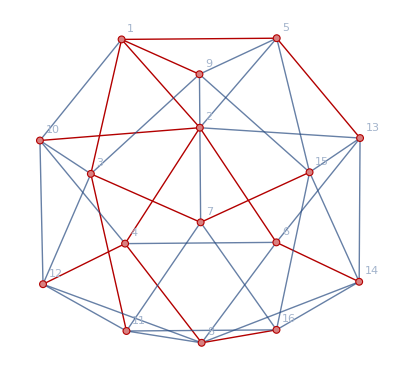

```mathematica
HighlightGraph[G1,gi,GraphHighlightStyle->"Thick",VertexLabels->"Name"]
```

Clean the data by removing those entries that are not containing the RC tree graph:

```mathematica
tmp=Position[IsSubtreeCH,False];
tmp
NAutomorphismGroupsCHClean=Delete[NAutomorphismGroupsCH,tmp];
IsSubtreeCHClean=Delete[IsSubtreeCH,tmp];
NEdgesCHClean=Delete[NEdgesCH,tmp];
IsThomsonGraphClean = Delete[IsThomsonGraph,tmp];
STATESClean = Delete[STATES,tmp];
CHMATClean =  Delete[CHMAT,tmp];
```

{{169},{482},{492},{514},{1234},{1478},{1647},{1863},{2051},{2220},{2454},{2501},{2664},{2683},{2696},{2860},{2918},{2971},{3325},{3527},{3778},{4008},{4073},{4338},{4354},{4564},{4768},{5055},{5066},{5741},{5990},{6032}}

Count how many adjacency graphs are not isomorphic to the Thomson graphs:

```mathematica
tmp=Position[IsThomsonGraphClean,False];
tmp//Length
```

2

Count the number of unique adjacency situations when the vertices are labeled. Does the number of possible adjacencies per state correlate with the probability of the state?

```mathematica
ExcludeID=Position[IsThomsonGraphClean,False];
EquivAdj=Table[0,{i,1,72}];
For[i=1, i≤72, i++,
id2=Flatten[Position[STATESClean,i]];
id2 = Cases[id2, Except[ExcludeID]];
tmp1=CHMATClean[[id2]];
tmp2=DeleteDuplicates[tmp1];
EquivAdj[[i]]=Length[tmp2];
]
```

Total number of unique adjacency matrices:

```mathematica
UniqueAdj=DeleteDuplicates[CHMATClean];
```

```mathematica
UniqueAdj//Length
```

1547

```mathematica
(16*16-16)/2-15
```

105

```mathematica
Binomial[105,(42-15)]
```

8769839154564131229033840

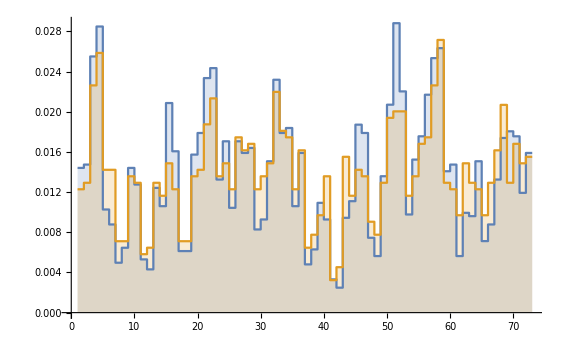

```mathematica
STATESThomson = Delete[STATESClean,Position[IsThomsonGraphClean,False]];
BC=BinCounts[STATESThomson,{0.5,72.5,1}];
ListStepPlot[{BC/Total[BC],EquivAdj/Total[EquivAdj]},Filling->Axis]
```

```mathematica
Export["processed_data_paul/adjac_counts_prob.mat",{BC, EquivAdj}];
```

```mathematica
Cases[NAutomorphismGroupsCH,24]//Length
```

3457

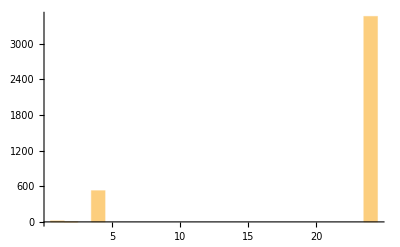

```mathematica
Histogram[NAutomorphismGroupsCH,{0.5,24.5,1},PlotRange->All]
```

```mathematica
3457/4000//N
```

0.86425

```mathematica
SDat=Table[{STATESClean[[i]],NAutomorphismGroupsCHClean[[i]]},{i,1,Length[STATESClean]}];
```

```mathematica
Histogram3D[SDat,{{0.5,72.5,1},{-0.5,24.5,1}}]
```

-Graphics3D-

## Spheres with equal radius: (Norbert’s N=4000 simulations)

```mathematica
STATES=Round[Import["processed_data_norbert/Equil_states.mat"][[1,1]]];
STATESOLD=Round[Import["processed_data_norbert/states.mat"][[1,1]]];
CHADJ=Import["processed_data_norbert/Equil_CHAdjMatrix.mat"];
CHMAT=CHADJ[[1,1]];
```

Check that during equilibration no change of the 1D state occurred:

```mathematica
Select[STATES-STATESOLD,#!=0&]
```

{}

Use the convex hull adjacency matrices to analyze graph structures:

```mathematica
NAutomorphismGroupsCH=Table[0,{i,1,Length[CHMAT]}];
IsSubtreeCH=Table[0,{i,1,Length[CHMAT]}];
NEdgesCH=Table[0,{i,1,Length[CHMAT]}];
IsThomsonGraph=Table[0,{i,1,Length[CHMAT]}];
For[i=1,i≤Length[CHMAT],i++,
m=Round[CHMAT[[i]]];
G1=AdjacencyGraph[m];
a=GraphAutomorphismGroup[G1];
T1=IsomorphicGraphQ[ThomsonGraph,G1];
T2=IsomorphicGraphQ[ThomsonGraph2,G1];
IsThomsonGraph[[i]]=Or[T1,T2];
NAutomorphismGroupsCH[[i]]=GroupOrder[a];
IsSubtreeCH[[i]]=IsomorphicGraphQ[GRC,GraphIntersection[G1,GRC]];
NEdgesCH[[i]]=EdgeCount[G1];
];
```

Clean the data by removing those entries that are not containing the RC tree graph:

```mathematica
tmp=Position[IsSubtreeCH,False];
tmp
NAutomorphismGroupsCHClean=Delete[NAutomorphismGroupsCH,tmp];
IsSubtreeCHClean=Delete[IsSubtreeCH,tmp];
NEdgesCHClean=Delete[NEdgesCH,tmp];
IsThomsonGraphClean = Delete[IsThomsonGraph,tmp];
STATESClean = Delete[STATES,tmp];
CHMATClean =  Delete[CHMAT,tmp];
```

{{281},{337},{402},{466},{582},{1158},{1286},{1354},{1423},{1435},{1532},{1831},{2257},{2471},{2502},{2528},{2582},{2615},{2972},{3102},{3191},{3934},{3943}}

Count how many adjacency graphs are not isomorphic to the Thomson graphs:

```mathematica
tmp=Position[IsThomsonGraphClean,False];
tmp//Length
```

1

Count the number of unique adjacency situations when the vertices are labeled. Does the number of possible adjacencies per state correlate with the probability of the state?

```mathematica
ExcludeID=Position[IsThomsonGraphClean,False];
EquivAdj=Table[0,{i,1,72}];
For[i=1, i≤72, i++,
id2=Flatten[Position[STATESClean,i]];
id2 = Cases[id2, Except[ExcludeID]];
tmp1=CHMATClean[[id2]];
tmp2=DeleteDuplicates[tmp1];
EquivAdj[[i]]=Length[tmp2];
]
```

Total number of unique adjacency matrices:

```mathematica
UniqueAdj=DeleteDuplicates[CHMATClean];
```

```mathematica
UniqueAdj//Length
```

1334

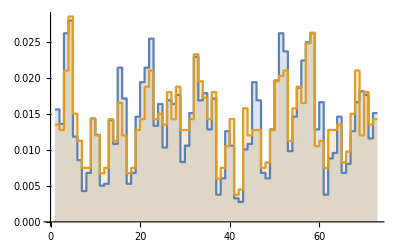

```mathematica
STATESThomson = Delete[STATESClean,Position[IsThomsonGraphClean,False]];
BC=BinCounts[STATESThomson,{0.5,72.5,1}];
ListStepPlot[{BC/Total[BC],EquivAdj/Total[EquivAdj]},Filling->Axis]
```

```mathematica
Export["processed_data_norbert/adjac_counts_prob.mat",{BC, EquivAdj}];
```

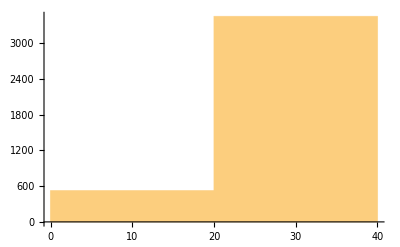

```mathematica
Histogram[NAutomorphismGroupsCHClean,PlotRange->All]
```

```mathematica
SDat=Table[{STATESClean[[i]],NAutomorphismGroupsCHClean[[i]]},{i,1,Length[STATESClean]}];
```

```mathematica
Histogram3D[SDat,{{0.5,72.5,1},{-0.5,24.5,1}}]
```

-Graphics3D-